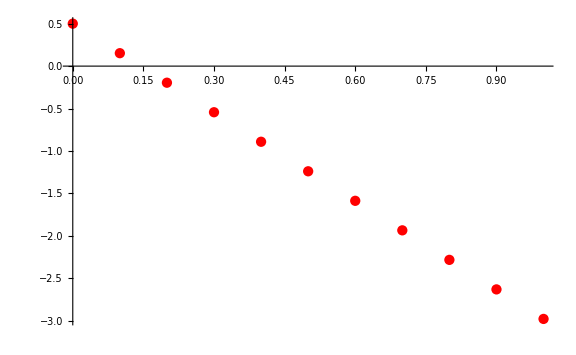

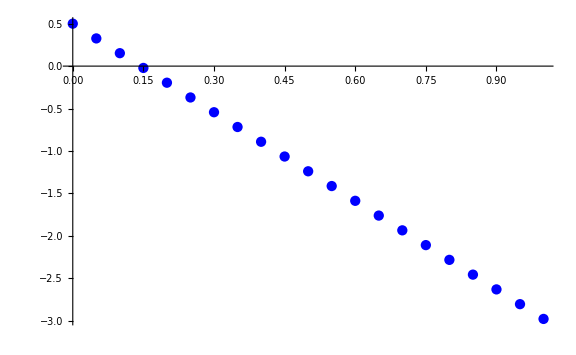

```mathematica
(*1*)
f[x_,y_]=1+4ySin[x]x-1.5y^2;
a=0;b=1;x0=0;y0=0;
(*А*)
h=0.1; n=(b-a)/h;
x=x0;y=y0;
eul=Table[{x,y}={x+h, y + h*f[x,y]},{i,n}];
eul=Prepend[eul,{x0,y0}];
i=2;
While[i <= n + 1, eul[[i,2]]=eul[[i-1,2]]+h/2*(f[eul[[i-1,1]],eul[[i-1,2]]]+f[eul[[i,1]],eul[[i,2]]]);
i++];
p1=ListPlot[eul,PlotStyle->Red,ImageSize->Large];
h=0.05;n=(b-a)/h;x=x0;y=y0;
eul=Table[{x,y}={x+h,y+h*f[x,y]},{i,n}];
eul=Prepend[eul,{x0,y0}];
i=2;
While[i <= n + 1, eul[[i,2]]=eul[[i-1,2]]+h/2*(f[eul[[i-1,1]],eul[[i-1,2]]]+f[eul[[i,1]],eul[[i,2]]]);
i++];
p2=ListPlot[eul, PlotStyle->Blue,ImageSize->Large];
Print[p1];
Print[p2];
```

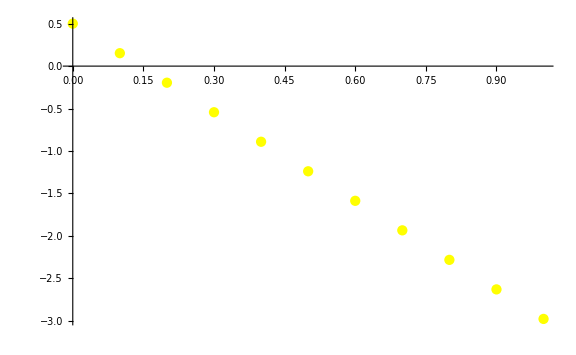

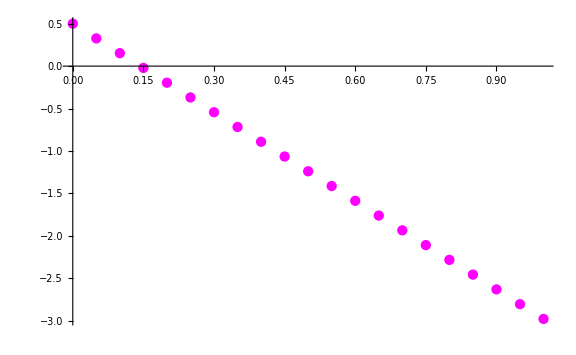

```mathematica
(*Б*)
h=0.1;n=(b-a)/h;
rynge=List[{x0,y0}];
x=x0;y=y0;
For[k = 1, k < n + 1, k++,
k1[x_, y_]=h*f[x,y];
k2[x_,y_]=h*f[x+h/2, y + k1[x,y]/2];
k3 [x_,y_]=h*f[x+h/2, y + k2[x,y]/2];
k4[x_,y_]=h*f[x+h, y+k3[x,y]];
x=x+h; y= y + (k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
rynge = Append[rynge, {x,y}]];
p3=ListPlot[rynge,ImageSize->Large,PlotStyle->Yellow];
h = 0.05; n = (b-a)/h;
rynge = List[{x0,y0}];
x = x0; y = y0;
For[k = 1, k < n + 1, k++,
k1[x_, y_]=h*f[x,y];
k2[x_,y_]=h*f[x+h/2, y + k1[x,y]/2];
k3 [x_,y_]=h*f[x+h/2, y + k2[x,y]/2];
k4[x_,y_]=h*f[x+h, y+k3[x,y]];
x=x+h; y= y + (k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
rynge = Append[rynge, {x,y}]];
p4=ListPlot[rynge,ImageSize->Large,PlotStyle->Magenta];
Print[p3];
Print[p4];
```

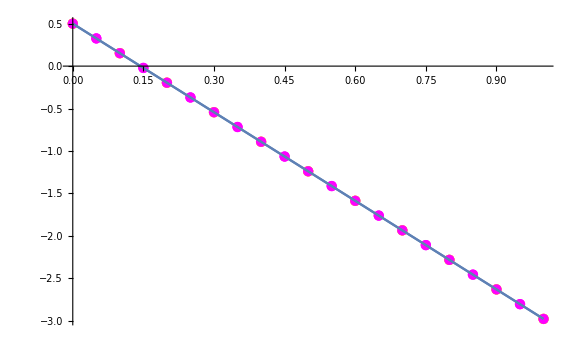

```mathematica
(*В*)
Clear[x,y];
DS = DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x];
y1[x_]=y[x]/.Flatten[DS];
NDS=NDSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],{x,0,1}];
p5=Plot[y1[x],{x,0,1},ImageSize->Large];
p6=Plot[Evaluate[y[x]/.NDS],{x,0,1},ImageSize->Large];
Show[p1,p2,p3,p4,p5,p6]
```

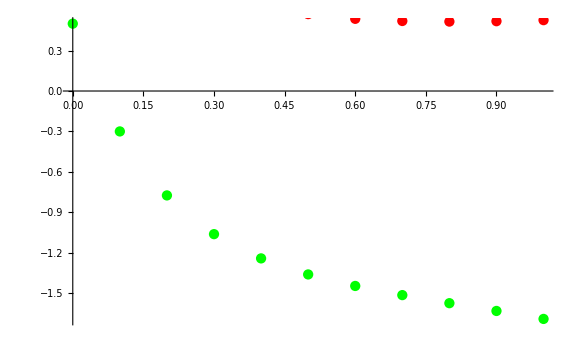

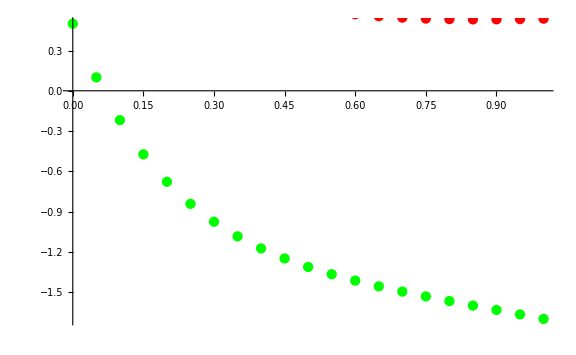

```mathematica
(*2*)
f[x_,{y_,z_}]={3z+y^2, 7z};x0=0;Temp0={1,0};h=0.1;n=(b-a)/h;
x=x0;Temp=Temp0;
(*A*)
eul = Table[{x,Temp}={x+h, Temp+ h*f[x,Temp]},{i,n}];
eul = Prepend[eul, {x0,Temp0}];
i=1;
eul1=eul;
While[i < n +2, eul1[[i]]=eul[[i,2]];i++];
p1 = Table[{eul[[i,1]],eul1[[i,1]]},{i,1,n+1}]; p2 = Table[{eul[[i,1]],eul1[[i,2]]},{i,1,n+1}];
Show[ListPlot[p1,PlotStyle->Green],ListPlot[p2, PlotStyle->Red],ImageSize->Large]
h=0.05; n = (b-a)/h;
x=x0; Temp = Temp0;
eul = Table[{x,Temp}={x+h, Temp+ h*f[x,Temp]},{i,n}];
eul = Prepend[eul, {x0,Temp0}];
i = 1;
eul1=eul;
While[i < n +2, eul1[[i]]=eul[[i,2]];i++];
p3=Table[{eul[[i,1]],eul1[[i,1]]},{i,1,n+1}]; 
p4=Table[{eul[[i,1]],eul1[[i,2]]},{i,1,n+1}];
Show[ListPlot[p3,PlotStyle->Green],ListPlot[p4, PlotStyle->Red],ImageSize->Large]
```

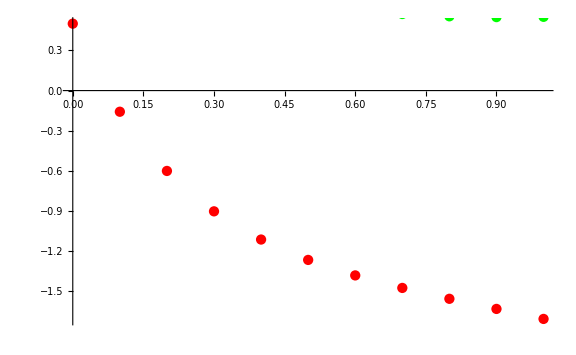

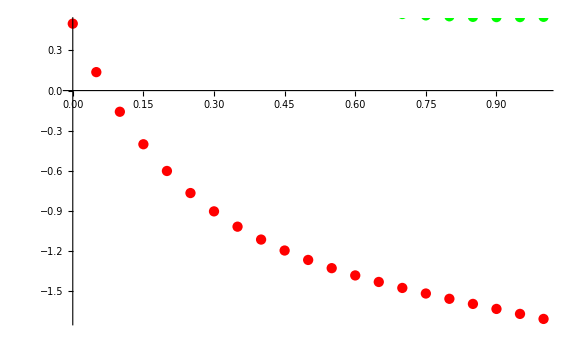

```mathematica
(*Б*)
h = 0.1; n = (b-a)/h;
rynge = List[{x0,Temp0}];
x = x0; Temp= Temp0;
For[k = 1, k < n + 1, k++,
k1[x_, {y_,z_}]=h*f[x,Temp];
k2[x_,{y_,z_}]=h*f[x+h/2, Temp + k1[x,Temp]/2];
k3 [x_,{y_,z_}]=h*f[x+h/2, Temp + k2[x,Temp]/2];
k4[x_,{y_,z_}]=h*f[x+h, Temp+k3[x,Temp]];
x=x+h; Temp= Temp + (k1[x,Temp]+2*k2[x,Temp]+2*k3[x,Temp]+k4[x,Temp])/6;
rynge = Append[rynge, {x,Temp}]];
i = 1;
rynge1 = rynge;
While[i < n +2, rynge1[[i]]=rynge[[i,2]];i++]
p5 = Table[{rynge[[i,1]],rynge1[[i,1]]},{i,1,n+1}]; p6 = Table[{rynge[[i,1]],rynge1[[i,2]]},{i,1,n+1}];
Show[{ListPlot[p5,ImageSize->Large, PlotStyle->Red], ListPlot[p6,ImageSize->Large, PlotStyle->Green]}]
h = 0.05; n = (b-a)/h;
rynge = List[{x0,Temp0}];
x = x0; Temp= Temp0;
For[k = 1, k < n + 1, k++,
k1[x_, {y_,z_}]=h*f[x,Temp];
k2[x_,{y_,z_}]=h*f[x+h/2, Temp + k1[x,Temp]/2];
k3 [x_,{y_,z_}]=h*f[x+h/2, Temp + k2[x,Temp]/2];
k4[x_,{y_,z_}]=h*f[x+h, Temp+k3[x,Temp]];
x=x+h; Temp= Temp + (k1[x,Temp]+2*k2[x,Temp]+2*k3[x,Temp]+k4[x,Temp])/6;
rynge = Append[rynge, {x,Temp}]];
i = 1;
rynge1 = rynge;
While[i < n +2, rynge1[[i]]=rynge[[i,2]];i++]
p7 = Table[{rynge[[i,1]],rynge1[[i,1]]},{i,1,n+1}]; p8 = Table[{rynge[[i,1]],rynge1[[i,2]]},{i,1,n+1}];
Show[{ListPlot[p7,ImageSize->Large, PlotStyle->Red], ListPlot[p8,ImageSize->Large, PlotStyle->Green]}]
```

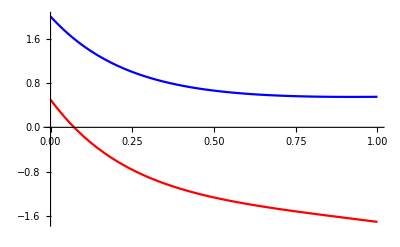

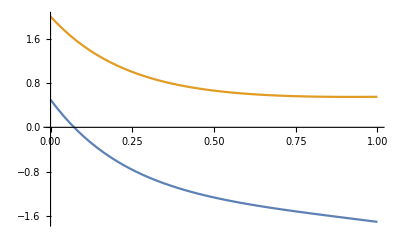

```mathematica
(*B*)
Clear[y,z,x];
eqn1=y'[x]==3*z[x]+y[x]^2;
eqn2=z'[x]==-y[x]-3*z[x];
ics={y[0]==0.5,z[0]==2};
sol=DSolve[{eqn1,eqn2,ics},{y[x],z[x]},x];
p9 = Plot[Evaluate[{y[x],z[x]}/. sol],{x,0,1}, PlotStyle->{Red, Blue}];
T=Table[Evaluate[{y[x],z[x]}/. sol], {x, 0, 1, 0.05}];
Clear[y, x, z]
eqn1=y'[x]==2-5*z[x];
eqn2=z'[x]==-y[x]-3*z[x];
ics={y[0]==0.5,z[0]==2};
sol=NDSolve[{eqn1,eqn2,ics},{y,z},{x,0,1}];
p10 = Plot[Evaluate[{y[x],z[x]}/. sol],{x,0,1}];
Print[p9];
Print[p10];
```

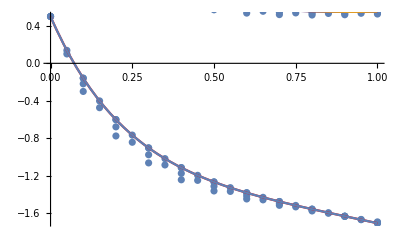

```mathematica
Show[ListPlot[p1],ListPlot[p2],ListPlot[p3],ListPlot[p4],ListPlot[p5],ListPlot[p6],ListPlot[p7],ListPlot[p8],p9,p10,ImageSize->Full]
```